```mathematica
Clear["Global`*"];
<<"/home/docencia/Downloads/RRT-caso1_MM1/RandomData.m"
<<"/home/docencia/Downloads/RRT-caso2_ARQ/drawTx.m"
```

Mi paquete sera: {tiempo_llegada,tasa_servicio,número_sec,error,num_rep}
Tasa de servicio 9600 --> un segundo
Modulo de DrawWin es ancho de la ventana, hasta que numero cuenta.

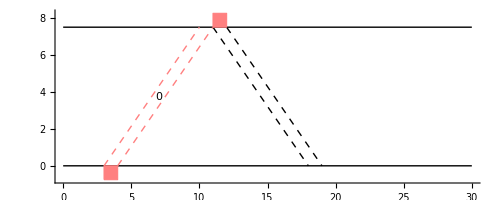

```mathematica
paquete={3,9600,0,0,0};
SetIniParDraw[7,1];
Show[DrawWin[0,30,5], DrawPacketTx[paquete]]
```

Stop and Wait habiendo siempre un paquete para entrar.

```mathematica
transtime=3;
servicetime=1;
longpack=19200;
listadepaquetes = Table[{n*(2*transtime+longpack/9600+servicetime),longpack,n,0,0},{n,0,14}];
SetIniParDraw[transtime,servicetime];
Manipulate[Show[DrawWin[origin,ww,15],Map[ DrawPacketTx[#]&,listadepaquetes]],{origin ,0 ,150-ww},{ww,10,50}]
```

Stop and Wait pero con tasas de llegada y servicio

```mathematica
GetInTime[arriv_,serv_,prop_,ack_]:= Module[{i,intime},i=0;intime={arriv[[1]]};For[i=2, i<Length[arriv],i++;intime=Join[intime,{intime[[i-1]]+serv[[i-1]]*9600+prop*2+ack}]];Return[intime]];
CreaPaquetes[intime_,serv_,num_]:= Module[{i,listapaq,n},n=0;For[i=1, i<Length[intime], i++;listapaq=Join[listapaq,{intime[[i]],serv[[i]],n,0,0}];If[n==num-1,n=0,n++];];Return[listapaq]];
```

```mathematica
lamda=90; mu=100; numPaquetes=25;
InterArrivalsTime=Table[RandomExp[lamda],numPaquetes];
ArrivalsTime=Accumulate[InterArrivalsTime];
ServTime=Table[RandomExp[mu],numPaquetes];
prop=0.05;ack=0.004;
insertions=GetInTime[ArrivalsTime,ServTime,prop,ack]
paquetes=CreaPaquetes[insertions,ServTime,8];
SetIniParDraw[prop,ack];
```

Part::partw: Part 2 of {0.0022654} does not exist.

Part::partw: Part 3 of {0.0022654,111.182+{0.0022654}⟦2⟧} does not exist.

Part::partw: Part 4 of {0.0022654,111.182+{0.0022654}⟦2⟧,29.9012+{0.0022654,111.182+{0.0022654}⟦2⟧}⟦3⟧} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Manipulate[Show[DrawWin[origin,ww,8],Map[DrawPacketTx[#]&,paquetes]],{origin,0,1-ww},{ww,0.01,0.2}]
```